# Mutual Information

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dir ="../AnalysisData/best_categ_pass_agent/";
(*dir = "../AnalysisData/best_offset/";*)
```

## By Subtasks

### Over time

```mathematica
aaO=Import[StringJoin[dir,"mi_size_inT_A_avoid.dat"]];
acO=Import[StringJoin[dir,"mi_size_inT_A_pass.dat"]];
baO=Import[StringJoin[dir,"mi_size_inT_B_avoid.dat"]];
bcO=Import[StringJoin[dir,"mi_size_inT_B_catch.dat"]];
```

```mathematica
ListLinePlot[Transpose[mi1]]
```

### Time-averaged

```mathematica
aaT=Flatten[Import[StringJoin[dir,"mi_size_tavg_A_avoid.dat"]]];
acT=Flatten[Import[StringJoin[dir,"mi_size_tavg_A_pass.dat"]]];
baT=Flatten[Import[StringJoin[dir,"mi_size_tavg_B_avoid.dat"]]];
bcT=Flatten[Import[StringJoin[dir,"mi_size_tavg_B_catch.dat"]]];
```

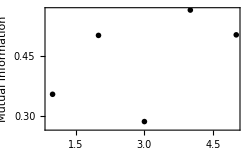

```mathematica
ListPlot[mi1,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotStyle->Black,PlotMarkers->{●}]
```

## By Tasks

### Over time

```mathematica
aO=Import[StringJoin[dir,"mi_size_inT_A_both.dat"]];
bO=Import[StringJoin[dir,"mi_size_inT_B_both.dat"]];
```

### Time-averaged

```mathematica
aT=Flatten[Import[StringJoin[dir,"mi_size_tavg_A_both.dat"]]];
bT=Flatten[Import[StringJoin[dir,"mi_size_tavg_B_both.dat"]]];
```

```mathematica
ListPlot[mi1,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotStyle->Black,PlotMarkers->{●}]
```

-Graphics-

## All data

### Over time

```mathematica
cO=Import[StringJoin[dir,"mi_size_inT_both_both.dat"]];
```

### Time-averaged

```mathematica
cT=Flatten[Import[StringJoin[dir,"mi_size_tavg_both_both.dat"]]];
```

```mathematica
ListPlot[mi1,PlotRange->All,Frame->True,FrameLabel->{"Neuron","Mutual Information"},ImageSize->250,PlotStyle->Black,PlotMarkers->{●}]
```

-Graphics-